# 2. teden

2. in 3. 3. 2021

## Naloga 1

Izračunaj števili e in π na 1000 decimalk.

```mathematica
N[Pi,1000]
N[E,1000]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420199

2.718281828459045235360287471352662497757247093699959574966967627724076630353547594571382178525166427427466391932003059921817413596629043572900334295260595630738132328627943490763233829880753195251019011573834187930702154089149934884167509244761460668082264800168477411853742345442437107539077744992069551702761838606261331384583000752044933826560297606737113200709328709127443747047230696977209310141692836819025515108657463772111252389784425056953696770785449969967946864454905987931636889230098793127736178215424999229576351482208269895193668033182528869398496465105820939239829488793320362509443117301238197068416140397019837679320683282376464804295311802328782509819455815301756717361332069811250996181881593041690351598888519345807273866738589422879228499892086805825749279610484198444363463244968487560233624827041978623209002160990235304369941849146314093431738143640546253152096183690888707016768396424378140592714563549061303107208510383750510115747704171898610687396965521267154688957035035

Določi 5., 100. in 443. decimalko števila π.

```mathematica
N[Pi,5]
```

3.1416

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
N[Pi,443]
```

3.1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679821480865132823066470938446095505822317253594081284811174502841027019385211055596446229489549303819644288109756659334461284756482337867831652712019091456485669234603486104543266482133936072602491412737245870066063155881748815209209628292540917153643678925903600113305305488204665213841469519415116094330572703657595919530921861173819326117931

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato s pomočjo definicije spremenljivke x. Spremenljivko x na koncu pobriši.
; ti ne izpiše rezultata ko pogneš

```mathematica
x = 1 / Sqrt[E] + 1/ Sqrt[Pi];
```

```mathematica
1 + x + x^2 + x^3
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

```mathematica
1 + x + x^2 + x^3 /. x ->2 / Sqrt[E] + 1/ Sqrt[Pi]
```

1+1/(√ⅇ)+(1/(√ⅇ)+1/(√π))^2+(1/(√ⅇ)+1/(√π))^3+1/(√π)

```mathematica
x =.
```

```mathematica
1 + x + x^2 + x^3
```

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).

```mathematica
Sin[Pi/8] + Cos[Pi/8]//FullSimplify
```

√(1+1/(√2))

Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše:

Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]]).

```mathematica
niz = "Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]])."
```

Vsota sin(π/8) + cos(π/8) je enaka √(1 + FractionBox[1, SqrtBox[2]]).

## Naloga 3

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?

Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

```mathematica
niz = "Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk."
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

Poskusi definirati zgornji niz še brez direktnega vnašanja števila 668 v niz. Nasvet: TemplateApply.

```mathematica
TemplateApply["Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = <*249+419*> jabolk."]
```

Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.

## Naloga 4

Definiraj funkcijo f(x)=x^2+3x+2+sin(x).

```mathematica
f[x_]:= x^2 + 3x + 2 +Sin[x]
```

Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).

```mathematica
f[3]+f[4]
(3 // f) + (4//f)
```

50+Sin[3]+Sin[4]

50+Sin[3]+Sin[4]

Nariši graf funkcije f na intervalu [-10,10].

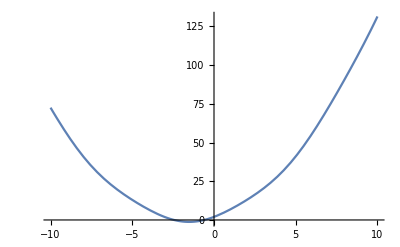

```mathematica
Plot[f[t],{t,-10,10}]
```

Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot čisto funkcijo.

```mathematica
g =#^2 + 3# + 2 +Sin[#] &
```

#1^2+3 #1+2+Sin[#1]&

```mathematica
g[5]
```

42+Sin[5]

Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot čisto funkcijo.

```mathematica
h1[x_,y_] := (f[x] + g[y])^2
h1[4,3]
```

(50+Sin[3]+Sin[4])^2

```mathematica
h2=(f[#1]+g[#2])^2 &
```

(f[#1]+g[#2])^2&

```mathematica
h2[4,3]
```

(50+Sin[3]+Sin[4])^2

## Naloga 5

Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.

```mathematica
Clear[f,g]
```

```mathematica
f[x_] := x^3+x+1
g[n_] := Mod[n,7]
```

Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.

```mathematica
seznam =Table[f[n],{n,1,100}]
```

{3,11,31,69,131,223,351,521,739,1011,1343,1741,2211,2759,3391,4113,4931,5851,6879,8021,9283,10671,12191,13849,15651,17603,19711,21981,24419,27031,29823,32801,35971,39339,42911,46693,50691,54911,59359,64041,68963,74131,79551,85229,91171,97383,103871,110641,117699,125051,132703,140661,148931,157519,166431,175673,185251,195171,205439,216061,227043,238391,250111,262209,274691,287563,300831,314501,328579,343071,357983,373321,389091,405299,421951,439053,456611,474631,493119,512081,531523,551451,571871,592789,614211,636143,658591,681561,705059,729091,753663,778781,804451,830679,857471,884833,912771,941291,970399,1000101}

```mathematica
test[n_] := (g[n] == 3)
```

```mathematica
test[29]
```

False

```mathematica
Select[seznam, test]
```

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

```mathematica
Select[Table[f[n],{n,1,100}],(g[#] == 3)&]
```

{3,31,521,1011,3391,4931,10671,13849,24419,29823,46693,54911,79551,91171,125051,140661,185251,205439,262209,287563,357983,389091,474631,512081,614211,658591,778781,830679,970399}

## Naloga 6

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

25

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode s pomočjo uporabe anonimnih funkcij. Poskusi najti kodo, ki vsebuje le 1 vrstico.

## Naloga 7

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

Kaj vrne naslednja koda? Pojasni!

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

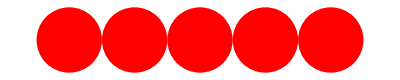

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).